```mathematica
(*Symmetric Confined Vortex Surface By Minimization *)

W = a DiagonalMatrix[{1,1,-2}];
```

```mathematica
NN[θ_,φ_] = {Sin[θ]Cos[φ], Sin[θ]Sin[φ], Cos[θ]};
```

```mathematica
DN[θ_,φ_] = D[NN[θ,φ],φ]
```

{-Sin[θ] Sin[φ],Cos[φ] Sin[θ],0}

```mathematica
II = NN[θ,φ].W.Cross[NN[θ,φ],DN[θ,φ]]//Simplify
```

-3 a Cos[θ] Sin[θ]^2

```mathematica
H1 = Integrate[-γ'[θ] r[θ]^3 2 Pi  II,{θ,0,Pi}]//Simplify
```

∫_0^π 6 a π Cos[θ] r[θ]^3 Sin[θ]^2 γ'[θ]ⅆθ

```mathematica
DNDN =DN[θ1,φ1].DN[θ2,φ2]//Simplify
```

Cos[φ1-φ2] Sin[θ1] Sin[θ2]

```mathematica
MyNorm[X_] := Sqrt[X[[1]]^2 + X[[2]]^2 + X[[3]]^2];
```

```mathematica
Coulomb[θ1_,φ1_,θ2_,φ2_, r1_, r2_] = DNDN/(8 Pi MyNorm[r1 NN[θ1,φ1] - r2 NN[θ2,φ2]])//FullSimplify
```

(Cos[φ1-φ2] Sin[θ1] Sin[θ2])/(8 π √(r1^2+r2^2-2 r1 r2 (Cos[θ1] Cos[θ2]+Cos[φ1-φ2] Sin[θ1] Sin[θ2])))

```mathematica
III[u_,v_] = Assuming[{u > v, v> 0},Integrate[Cos[x]/Sqrt[u - v Cos[x]],{x,0,2 Pi}]]//Simplify
```

(2 ((-u+v) √(u+v) EllipticE[-(2 v)/(u-v)]-√(u-v) (u+v) EllipticE[(2 v)/(u+v)]+u (√(u+v) EllipticK[-(2 v)/(u-v)]+√(u-v) EllipticK[(2 v)/(u+v)])))/(v √(u^2-v^2))

```mathematica
Assuming[{b  >0,b <1},Asymptotic[III[1,b],b->1]]
```

-(15 Log[1-b])/(4 √2)+(7 b Log[1-b])/(4 √2)

```mathematica
IntegralCoulomb[r1_,r2_,θ1_,θ2_]:= With [
{u =r1^2+r2^2-2 r1 r2 Cos[θ1] Cos[θ2],
v = 2 r1 r2 Sin[θ1] Sin[θ2]},
 2 Pi Sin[θ1] Sin[θ2]/(8 Pi)III[u,v] ];
```

```mathematica
H2 := Integrate[γ'[θ1]r[θ1]Integrate[γ'[θ2]r[θ2] 
IntegralCoulomb[r[θ1],r[θ2],θ1,θ2],{θ2,0,Pi}],{θ1,0,Pi}]
```

```mathematica
eps = 10^(-6);
```

```mathematica
IC[r1_,r2_,z1_, z2_]:= With [
{u =eps +r1^2+r2^2-2 r1 r2 z1 z2,
v = 2 r1 r2 Sqrt[(1-z1^2)(1-z2^2)]},
 Sqrt[(1-z1^2)(1-z2^2)]/4III[u,v] ];
```

```mathematica
rrzz = {r1,r2,z1,z2};
```

```mathematica
{tt,CompiledIC}=Timing@Compile[
{r1,r2,z1,z2},
IC[r1,r2,z1,z2],
"RuntimeOptions"->"EvaluateSymbolically"->False
];
```

```mathematica
CompiledIC[1.,0.1,0.5,0.2]
```

0.0582139

```mathematica
L = 10;
```

```mathematica
RR = r/@ Range[0,L];
GG = g/@ Range[0,L];
```

```mathematica
Vars = Join[RR,GG];
```

```mathematica
InitSub = (#->0)& /@Vars
```

{r[0]→0,r[1]→0,r[2]→0,r[3]→0,r[4]→0,r[5]→0,r[6]→0,r[7]→0,r[8]→0,r[9]→0,r[10]→0,g[0]→0,g[1]→0,g[2]→0,g[3]→0,g[4]→0,g[5]→0,g[6]→0,g[7]→0,g[8]→0,g[9]→0,g[10]→0}

```mathematica
DPL[l_,z_] =D[LegendreP[l,z],z];
```

```mathematica
II = .;
```

```mathematica
II[z_]= -3 z (1-z^2);
```

```mathematica
-3 z (1-z^2)
```

-3 z (1-z^2)

```mathematica
testG = Table[1,{l,0,L}];
testR = Table[0.1,{l,0,L}];
```

```mathematica
H1N=.;
H1N[gg_, rr_]:=2 Pi NIntegrate[
With[
{lp = Table[LegendreP[l,z],{l,0,L}], 
dlp=  Table[DPL[l,z],{l,0,L}]},
-gg.dlp E^(3rr.lp)  II[z]],{z,-1,1}];
```

```mathematica
H1N[testG,testR]
```

56.7565

```mathematica
H2N[gg_,rr_]:=2NIntegrate[
With[
{z2 = 2 t2 -1},
lp2 = Table[LegendreP[l,z2],{l,0,L}];
dlp2 = Table[DPL[l,z2],{l,0,L}];
r2 = E^(rr.lp2);
gg.dlp2 r2  
With[
{z1 = 2 t2 t -1},
lp1 = Table[LegendreP[l,z1],{l,0,L}];
dlp1 =Table[DPL[l,z1],{l,0,L}];
r1 = E^(rr.lp1);
gg.dlp1 r1  CompiledIC[ r1,r2,z1,z2]]
],{t,0.,1.},{t2,0.,1.},Method->"LocalAdaptive"];
```

```mathematica
H2N[testG,testR]
```

CompiledFunction::cfsa: Argument ⅇ^(0.1+«9»+0.1 (1-110 t t2+2970 t^2 t2^2-34320 t^3 t2^3+«6»+1969110 t^8 t2^8-923780 t^9 t2^9+184756 t^10 t2^10)) at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

5.15653

```mathematica
Conds = Flatten[{#<1,# > -1}& /@ RR]
```

{r[0]<1,r[0]>-1,r[1]<1,r[1]>-1,r[2]<1,r[2]>-1,r[3]<1,r[3]>-1,r[4]<1,r[4]>-1,r[5]<1,r[5]>-1,r[6]<1,r[6]>-1,r[7]<1,r[7]>-1,r[8]<1,r[8]>-1,r[9]<1,r[9]>-1,r[10]<1,r[10]>-1}

```mathematica
{r[0]<0.5,r[0]>-0.5,r[1]<0.5,r[1]>-0.5,r[2]<0.5,r[2]>-0.5,r[3]<0.5,r[3]>-0.5,r[4]<0.5,r[4]>-0.5,r[5]<0.5,r[5]>-0.5}
```

{r[0]<0.5,r[0]>-0.5,r[1]<0.5,r[1]>-0.5,r[2]<0.5,r[2]>-0.5,r[3]<0.5,r[3]>-0.5,r[4]<0.5,r[4]>-0.5,r[5]<0.5,r[5]>-0.5}

```mathematica
Sol= NMinimize[{Hold[H2N[GG,RR]+H1N[GG,RR]],Conds},Join[GG,RR],MaxIterations->100,AccuracyGoal->4]//Timing
```

CompiledFunction::cfsa: Argument ⅇ^(0.266236+0.510353 (-1+«1»)+«13»+0.561654 (1-110 t t2+«12»+184756 t^10 t2^10)) at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

```mathematica
RadiusFunc[z_] := With[
{lp = Table[LegendreP[l,z],{l,0,L}], 
rr =RR/.Sol[[2,2]]
},
E^(rr.lp)
];
```

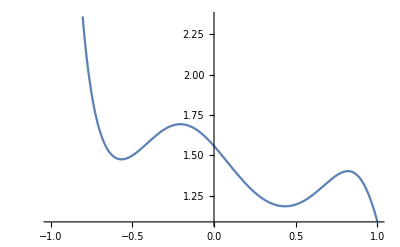

```mathematica
Plot[RadiusFunc[z],{z,-1,1}]
```

```mathematica
ParametricPlot3D[RadiusFunc[Cos[θ]] NN[θ,φ],{θ,0,Pi},{φ,-Pi,Pi},PlotRange->All, Boxed->False,Axes->None,PlotStyle->{Opacity[0.7],Green},MaxRecursion->4]
```

-Graphics3D-